```mathematica
(*************************)
n=10;
φ=50°;
R=7;
velčrk=6*20;
(*************************)
h=(R Cos[π/n])/Tan[φ];
grafika=Show[

Table[
Graphics3D[{
RGBColor[{0,1,1,1}],
EdgeForm[],

Polygon[{
{R Cos[(i-1)(2π)/n],R Sin[(i-1)(2π)/n],0},
{R Cos[i(2π)/n],R Sin[i(2π)/n],0},
{0,0,-h}
}]
}],
{i,n}],

Table[
Graphics3D[{
RGBColor[{1,0,0,.5}],
EdgeForm[],

Polygon[{
{0,0,-h}+RotationMatrix[i φ/50,{{0,0,1},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2}].{0,0,2},
{0,0,-h}+RotationMatrix[(i+1)φ/50,{{0,0,1},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2}].{0,0,2},
{0,0,-h}
}]
}],
{i,50}],

Table[
Graphics3D[{

If[i==25,Style[Text[
"α",

{0,0,-h}+.7RotationMatrix[i φ/50,{{0,0,1},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2}].{0,0,2}
],
RGBColor[{1,0,0}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],
Nothing
],
RGBColor[{1,0,0,1}],
EdgeForm[],

Tube[{
{0,0,-h}+RotationMatrix[i φ/50,{{0,0,1},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2}].{0,0,2},
{0,0,-h}+RotationMatrix[(i+1)φ/50,{{0,0,1},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2}].{0,0,2}
},.01]
}],
{i,50}],

Graphics3D[{

Style[Text[
"h",
{-.5,0,-h/2}
],
RGBColor[.3{1,1,1}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],
Thickness[.003],
RGBColor[.3{1,1,1}   ],
Tube[{{0,0,-h},{0,0,0}},.03]


}],

Graphics3D[{
Style[Text[
"R",
{R/2,0,.5}
],
RGBColor[{1,0,0}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],

RGBColor[{1,0,0}   ],
Tube[{{0,0,0},{R,0,0}},.03]

}],

Graphics3D[{
Dotted,
RGBColor[{0,0,0}   ],
Tube[{{0,0,-h},{0,0,-h}+({R,0,h}+{R Cos[(2π)/n],R Sin[(2π)/n],h})/2},.01]

}],

Boxed->False,
(*ViewPoint->20 {Cos[φ],Sin[φ],.3},
SphericalRegion->Sphere[{0,0,0},1],

PlotRange->{{,},{,},{,}},*)
ImageSize->6{1920,1080}
];
Export["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\piramidni original.png",%]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\piramidni original.png

```mathematica
.005]

}]
}]
}]
```

```mathematica
Graphics3D[{
.005]

}]
}]
}]
```

```mathematica
Graphics3D[{
.005]

}]
}]
}]
```

```mathematica
Graphics3D[{
RGBColor[0,1,1,1],
```

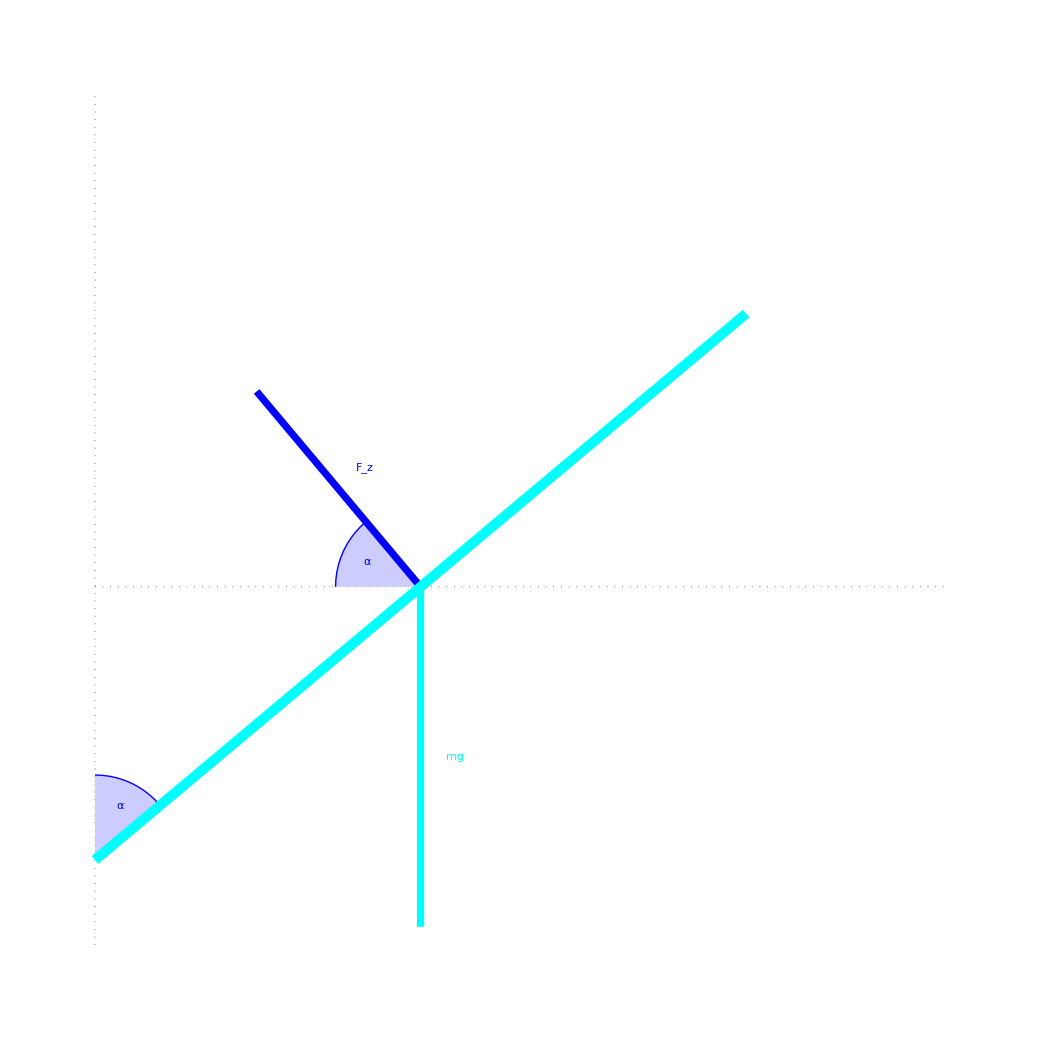

```mathematica
α=50°;
velčrk=30;
Show[
Graphics[{
Dotted,
RGBColor[0,0,0],
Thickness[.0005],
Line[{{0,0},{0,1}}]
}],

Graphics[{
Dotted,
RGBColor[0,0,0],
Thickness[.0005],
Line[{{0,.1+.5Cos[α]},{1,.1+.5Cos[α]}}]
}],

Graphics[{
RGBColor[{.8,.8,1}],
Disk[{0,.1},.1,{π/2-α,π/2}
]}],

Graphics[{


Style[Text[
"α",
{0,.1}+.7*.1*{Cos[(π-α)/2],Sin[(π-α)/2]}
],
RGBColor[{0,0,1}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],


RGBColor[{0,0,1}],
Circle[{0,.1},.1,{π/2-α,π/2}
]}],


Graphics[{

RGBColor[{.8,.8,1}],
Disk[{0,.1}+.5{Sin[α],Cos[α]},.1,{π-α,π}
]}],


Graphics[{


Style[Text[
"α",
{0,.1}+.5{Sin[α],Cos[α]}+.7*.1*{Cos[π-α/2],Sin[π-α/2]}
],
RGBColor[{0,0,1}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],


RGBColor[{0,0,1}],
Circle[{0,.1}+.5{Sin[α],Cos[α]},.1,{π-α,π}
]}],



Graphics[{


Style[Text[
"F_z",
Total[{{0,.1}+.5{Sin[α],Cos[α]},{0,.1}+.5{Sin[α],Cos[α]}+.3{-Cos[α],Sin[α]}}]/2+.04{Sin[α],Cos[α]}
],
RGBColor[{0,0,1}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],


RGBColor[0,0,1],
Thickness[.005],
Arrowheads[.03],
Arrow[{{0,.1}+.5{Sin[α],Cos[α]},{0,.1}+.5{Sin[α],Cos[α]}+.3{-Cos[α],Sin[α]}}]
}],


Graphics[{


Style[Text[
"mg",
Total[{{0,.1}+.5{Sin[α],Cos[α]},{0,.1}+.5{Sin[α],Cos[α]}+.4{0,-1}}]/2+.04{1,0}
],
RGBColor[{0,1,1}   ],velčrk,Bold,FontFamily->"Comic Sans MS"],


RGBColor[0,1,1],
Thickness[.005],
Arrowheads[.03],
Arrow[{{0,.1}+.5{Sin[α],Cos[α]},{0,.1}+.5{Sin[α],Cos[α]}+.4{0,-1}}]
}],

Graphics[{
RGBColor[0,1,1],
Thickness[.007],
Line[{{0,.1},{0,.1}+{Sin[α],Cos[α]}}]
}]


]
```

```mathematica
Export["c:\\Users\\gal\\Downloads\\rn.aviončki\\grafi\\sile na piramidno letalo.pdf",%]
```

c:\Users\gal\Downloads\rn.aviončki\grafi\sile na piramidno letalo.pdf